## The Mandelbrot and the Julia Set F. I. Giasemis

### The Mandelbrot Set

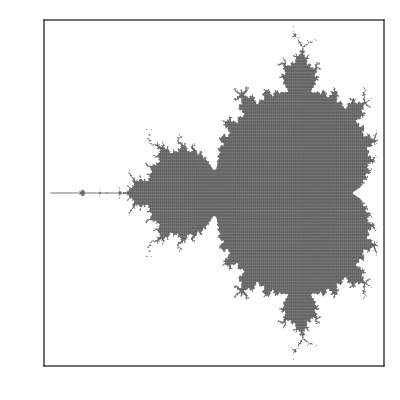

```mathematica
points={};
For[i=-2,i<2,i+=.005,
For[j=-2,j<2,j+=.005,
c=i+I j;
z=0;
diverge=False;
For[n=1,n<20,n++,
z=z^2+c;
]
If[Abs[z]<2,
AppendTo[points,{i,j}]
]
]
]
ListPlot[points,AspectRatio->1,Frame->True,Axes->False,FrameTicks->None,PlotStyle->{Black,PointSize[0.001]}]
```

### The Julia Set

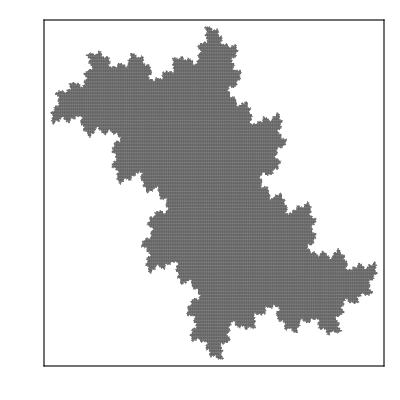
-Graphics-c = 0.6 i

```mathematica
points={};
For[i=-2,i<2,i+=.005,
For[j=-2,j<2,j+=.005,
z=i+I j;
c=.6 I;
diverge=False;
For[n=1,n<20,n++,
z=z^2+c;
]
If[Abs[z]<1,
AppendTo[points,{i,j}]
]
]
]
Labeled[ListPlot[points,AspectRatio->1,Frame->True,Axes->False,FrameTicks->None,PlotStyle->{Black,PointSize[0.001]}],"c = 0.6 i"]
```

### The Julia Set

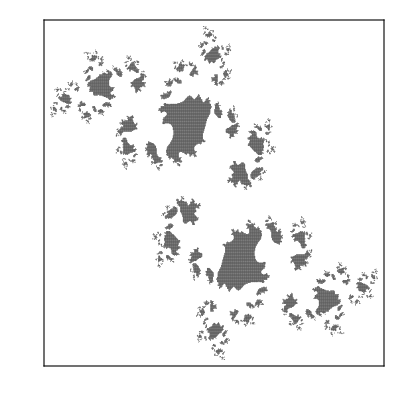
-Graphics-c = 0.7 i

```mathematica
points={};
For[i=-2,i<2,i+=.005,
For[j=-2,j<2,j+=.005,
z=i+I j;
c=.7 I;
diverge=False;
For[n=1,n<20,n++,
z=z^2+c;
]
If[Abs[z]<1,
AppendTo[points,{i,j}]
]
]
]
Labeled[ListPlot[points,AspectRatio->1,Frame->True,Axes->False,FrameTicks->None,PlotStyle->{Black,PointSize[0.001]}],"c = 0.7 i"]
```

### The Julia Set

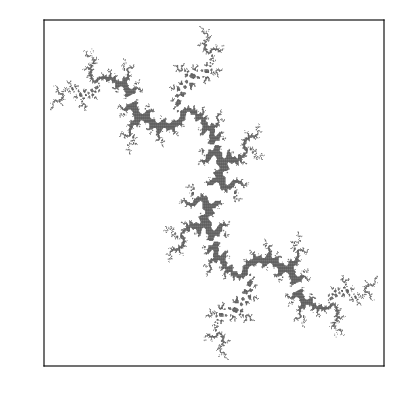
-Graphics-c = 0.8 i

```mathematica
points={};
For[i=-2,i<2,i+=.005,
For[j=-2,j<2,j+=.005,
z=i+I j;
c=.8 I;
diverge=False;
For[n=1,n<20,n++,
z=z^2+c;
]
If[Abs[z]<1,
AppendTo[points,{i,j}]
]
]
]
Labeled[ListPlot[points,AspectRatio->1,Frame->True,Axes->False,FrameTicks->None,PlotStyle->{Black,PointSize[0.001]}],"c = 0.8 i"]
```